```mathematica
(* MA39110 / Assignment 2.2 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=1;h=(xf-x0)/n;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X =Table[x0+x*h,{x,1,n-1}];
B =Table[-4*(x0+x*h),{x,1,n-1}];
For[i=1,i<n,i++,
{
A[[i,i]]=-(2+(2/(h^2)));
If[i≠1,A[[i,i-1]]=(1/h^2)+X[[i]]/h];
If[i≠n-1,A[[i,i+1]]=(1/h^2)-X[[i]]/h];
}];
A[[1,1]]=A[[1,1]]+((1/h^2)+X[[1]]/h)*(4/(2*h+3));
A[[1,2]]=A[[1,2]]-((1/h^2)+X[[1]]/h)*(1/(2*h+3));
A[[n-1,n-1]]=A[[n-1,n-1]]+((1/h^2)-X[[n-1]]/h)*(-4/(4*h-3));
A[[n-1,n-2]]=A[[n-1,n-2]]+((1/h^2)-X[[n-1]]/h)*(1/(4*h-3));
B[[n-1]]=B[[n-1]]-(1/h^2-X[[n-1]]/h)*(2*h/(4*h-3));
Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B]];
```

```mathematica
sol=Model[10];
solt=DSolve[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[x],x]
err1=Abs[DSolveValue[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[X],x]-sol];
perr1 = ListPlot[Transpose[{X,err1}],PlotStyle->Red];
N[Max[err1]]
p1=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style["h=0.1",FontSize->18],PlotStyle->Black]},{ListPlot[Transpose[{X,sol}],PlotStyle->Red]}];
```

{{y[x]→ⅇ^(x^2)+x}}

0.748796

```mathematica
sol=Model[50];
err2=Abs[DSolveValue[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[X],x]-sol];
perr2 = ListPlot[Transpose[{X,err2}],PlotStyle->Blue];
N[Max[err2]]
p2=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style["h=0.1/5",FontSize->18],PlotStyle->Black]},{ListPlot[Transpose[{X,sol}],PlotStyle->Blue]}];
```

0.0328078

```mathematica
sol=Model[100];
err3=Abs[DSolveValue[{y''[x]-2*x*y'[x]-2*y[x]==-4*x,y[0]-y'[0]==0,2*y[1]-y'[1]==1},y[X],x]-sol];
perr3=ListPlot[Transpose[{X,err3}],PlotStyle->Green];
N[Max[err3]]
p3=Show[{Plot[Evaluate[y[x]/.solt],{x,x0,xf},PlotLabel->Style["h=0.1/10",FontSize->18],PlotStyle->Black]},{ListPlot[Transpose[{X,sol}],PlotStyle->Green]}];
```

0.00853588

3.66326

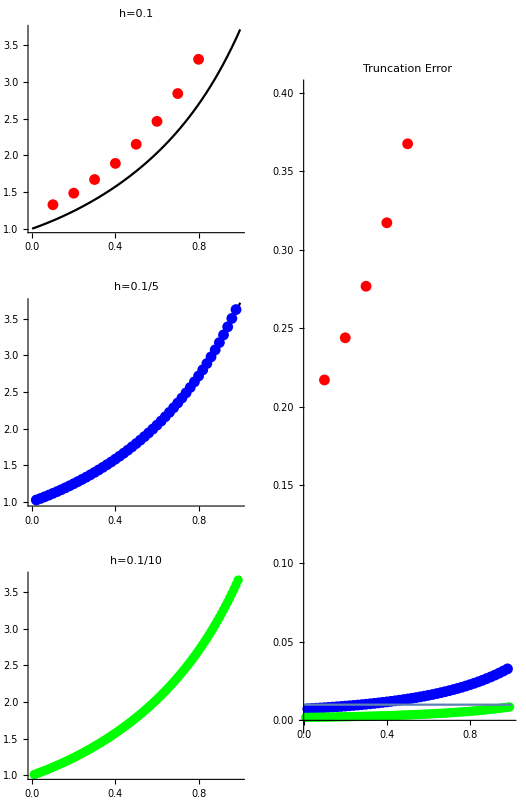

```mathematica
p4=Show[{perr1},{perr2},{perr3},{Plot[y[x]=10^-2,{x,0,1}]},PlotLabel->Style["Truncation Error",FontSize->18],PlotRange->{{0,1},{0,0.4}},AspectRatio->3];
N[sol[[-1]]]
GraphicsGrid[{{p1,p4},{p2,SpanFromAbove},{p3,SpanFromAbove}}]
```